```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
data = Import["solution.dat"];
sumenergy = Import["conserv_energy.dat"];
Length@data
```

3000

```mathematica
dataT=Partition[data,10];
dataXtemp=({#1[[1]],#1[[3]]}&/@#)&/@dataT;
dataTime =DeleteDuplicates[ #[[1,2]]&/@dataT];
sumenergy = Flatten@sumenergy;
TempMax =Max[Flatten@DeleteDuplicates[(#1[[3]]&/@#)&/@dataT]];
TempMin =Min[Flatten@DeleteDuplicates[(#1[[3]]&/@#)&/@dataT]];
```

```mathematica
ListPlot3D[data,ColorFunction->"TemperatureMap",PlotRange->Full,AxesLabel->{"x","t","T"}]
```

-Graphics3D-

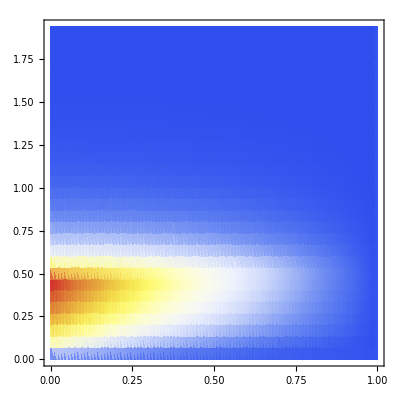

```mathematica
ListDensityPlot[data,ColorFunction->"TemperatureMap",PlotRange->All]
```

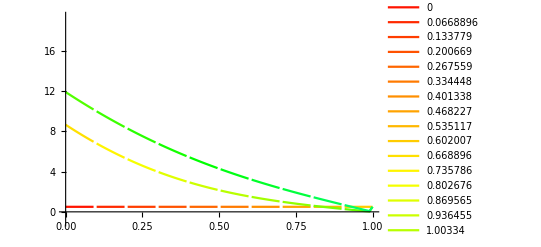

```mathematica
Show[Table[ListLinePlot[dataXtemp[[i]],PlotRange->{{0,1},{TempMin-1,TempMax+1}},PlotStyle->{Hue[(2i)/(5*Length@dataTime)]},PlotLegends->{dataTime[[i]]}],{i,1,Length@dataTime}]]
```

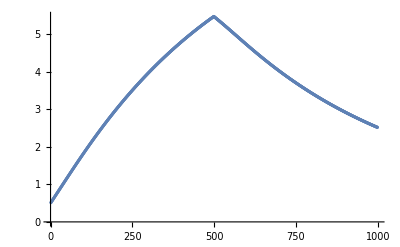

```mathematica
ListPlot[sumenergy]
```